```mathematica
(*Parameters and Constants*)
Avagadro=6.022142*10^23;
ze=2.42*10^-10;  (*bond distance 2.42 A in m *)
Ebond=300; (*bond Energy 300 kJ/mol *)
κ=2.55*10^10; (*decay factor in 1/angstrom*)
m1=12/Avagadro; (* weight of One Carbon Atom *) 
IVel=1; (* Initial Velocity of 1DOF model *)
IPos=ze;  (*Initial Position of 1DOF atom *)
endtime=N[10^-7]; (*Simulation End Time*)

(*Formulas And Calculations*)
L=-Ebond*(2*(ze/z)^6-(ze/z)^12); 
V=-Ebond*(2*Exp[-κ(z-ze)]-Exp[-2*κ(z-ze)]);
Va=V/Avagadro;
Fm=D[V,z]/Avagadro;

EqsOneDOF={m1*z1''[t]+(Fm/.z->z1[t])==0,z1[0]==IPos,z1'[0]==IVel};
ETot=0.5*m1*z1'[t]^2+(Va/.z->z1[t])-0.5*m1*IVel^2-Va/.z->IPos;

solOneDOF=NDSolve[EqsOneDOF,z1,{t,0,endtime},MaxSteps->∞,PrecisionGoal->13,AccuracyGoal->13];



TIME=endtime;
fmax=3*10^11;
dt=1/fmax;
fnyq=fmax/2;
Sample=TIME/dt;
amp=Table[(z1[t]/.solOneDOF)[[1]],{t,0,TIME,dt}];
tempfft=Abs[Fourier[amp,FourierParameters->{1,-1}]]/Sample*2; 
fft=Table[ {N[(i-1)]/Sample*fmax,20*Log[10,tempfft[[i]]]} , {i,1,Round[Sample/2]}];
```

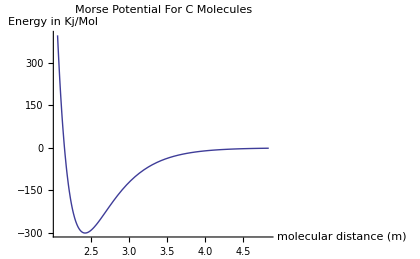
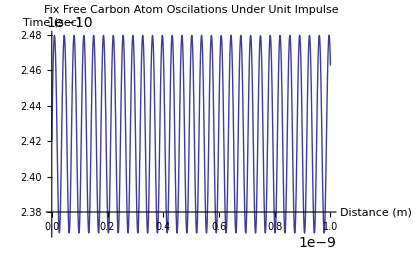
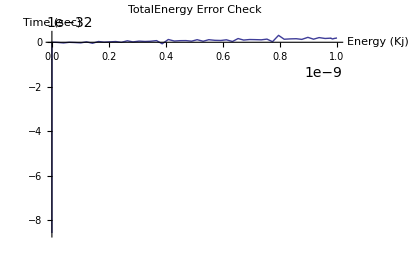
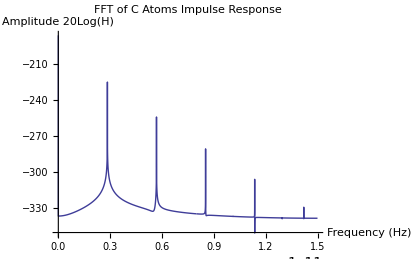
((*Parameters and Constants*),
Avagadro=6.022142*10^23;
ze=2.42*10^-10;  (*bond distance 2.42 A in m *)
Ebond=300; (*bond Energy 300 kJ/mol *)
κ=2.55*10^10; (*decay factor in 1/angstrom*)
m1=12/Avagadro; (* weight of One Carbon Atom *) 
IVel=1; (* Initial Velocity of 1DOF model *)
IPos=ze;  (*Initial Position of 1DOF atom *)
endtime=N[10^-7]; (*Simulation End Time*)

(*Formulas And Calculations*)
L=-Ebond*(2*(ze/z)^6-(ze/z)^12); 
V=-Ebond*(2*Exp[-κ(z-ze)]-Exp[-2*κ(z-ze)]);
Va=V/Avagadro;
Fm=D[V,z]/Avagadro 


Equations Of Motion = 
{1.99265×10^-23 z1''(t)-4.98162×10^-22 (5.1×10^10 ⅇ^(-5.1×10^10 (z1(t)-2.42×10^-10))-5.1×10^10 ⅇ^(-2.55×10^10 (z1(t)-2.42×10^-10)))==0,z1(0)==2.42×10^-10,z1'(0)==1}
-Graphics- -Graphics-


-Graphics- -Graphics-)

Options::opmix: Cannot mix streams and non-streams in StyleBox[{"(*Parameters and Constants*),\[IndentingNewLine]Avagadro=6.022142*10^23;\[IndentingNewLine]ze=2.42*10^-10;  (*bond distance 2.42 A in m *)\[IndentingNewLine]Ebond=300; (*bond Energy 300 kJ/mol *)\[IndentingNewLine]\[Kappa]=2.55*10^10; (*decay factor in 1/angstrom*)\[IndentingNewLine]m1=12/Avagadro; (* weight of One Carbon Atom *) \[IndentingNewLine]IVel=1; (* Initial Velocity of 1DOF model *)\[IndentingNewLine]IPos=ze;  (*Initial Position of 1DOF atom *)\[IndentingNewLine]endtime=N[10^-7]; (*Simulation End Time*)\[IndentingNewLine]\[IndentingNewLine](*Formulas And Calculations*)\[IndentingNewLine]L=-Ebond*(2*(ze/z)^6-(ze/z)^12); \[IndentingNewLine]V=-Ebond*(2*Exp[-\[Kappa](z-ze)]-Exp[-2*\[Kappa](z-ze)]);\[IndentingNewLine]Va=V/Avagadro;\[IndentingNewLine]Fm=D[V,z]/Avagadro \n\n", "Equations Of Motion = ", {-4.98162×10^-22\ (5.1×10^10\ Power[« 2 »] - 5.1×10^10\ Power[« 2 »]) + 1.99265×10^-23\ SuperscriptBox["z1", "′′", Rule[MultilineFunction, None]][t] == 0, z1[0] == 2.42×10^-10, SuperscriptBox["z1", "′", Rule[MultilineFunction, None]][0] == 1}, GraphicsBox[List[List[List[], List[], List[Hue[0.67, 0.6, 0.6], LineBox[List[Skeleton[250]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.618034]], Rule[Axes, True], Rule[AxesLabel, List[FormBox["\"molecular distance (m)\"", TraditionalForm], FormBox["\"Energy in Kj/Mol\"", TraditionalForm]]], Rule[AxesOrigin, List[2.×10^-10, 0]], Rule[ImageSize, 420], Rule[PlotLabel, FormBox["\"Morse Potential For C Molecules\"", TraditionalForm]], Rule[PlotRange, List[All, All]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]]\ GraphicsBox[List[List[List[], List[], List[Hue[0.67, 0.6, 0.6], LineBox[List[Skeleton[2258]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.618034]], Rule[Axes, True], Rule[AxesLabel, List[FormBox["\"Distance (m)\"", TraditionalForm], FormBox["\"Time (sec)\"", TraditionalForm]]], Rule[AxesOrigin, List[0, 2.38×10^-10]], Rule[ImageSize, 420], Rule[PlotLabel, FormBox["\"Fix Free Carbon Atom Oscilations Under Unit Impulse\"", TraditionalForm]], Rule[PlotRange, List[All, All]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]], "\n", GraphicsBox[List[List[List[], List[], List[Hue[0.67, 0.6, 0.6], LineBox[List[Skeleton[77]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.618034]], Rule[Axes, True], Rule[AxesLabel, List[FormBox["\"Energy (Kj)\"", TraditionalForm], FormBox["\"Time (sec)\"", TraditionalForm]]], Rule[AxesOrigin, List[0, 0]], Rule[ImageSize, 420], Rule[PlotLabel, FormBox["\"TotalEnergy Error Check\"", TraditionalForm]], Rule[PlotRange, List[All, All]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]]\ GraphicsBox[List[List[List[], List[], List[Hue[0.67, 0.6, 0.6], LineBox[List[Skeleton[15000]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.618034]], Rule[Axes, True], Rule[AxesLabel, List[FormBox["\"Frequency (Hz)\"", TraditionalForm], FormBox["\"Amplitude 20Log(H)\"", TraditionalForm]]], Rule[AxesOrigin, List[0, -350.]], Rule[ImageSize, 420], Rule[PlotLabel, FormBox["\"FFT of C Atoms Impulse Response\"", TraditionalForm]], Rule[PlotRange, List[All, All]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]]}, "MT"].

ReplaceAll::reps: StyleBox[{Options[{"(*Parameters and Constants*),\[IndentingNewLine]Avagadro=6.022142*10^23;\[IndentingNewLine]ze=2.42*10^-10;  (*bond distance 2.42 A in m *)\[IndentingNewLine]Ebond=300; (*bond Energy 300 kJ/mol *)\[IndentingNewLine]\[Kappa]=2.55*10^10; (*decay factor in 1/angstrom*)\[IndentingNewLine]m1=12/Avagadro; (* weight of One Carbon Atom *) \[IndentingNewLine]IVel=1; (* Initial Velocity of 1DOF model *)\[IndentingNewLine]IPos=ze;  (*Initial Position of 1DOF atom *)\[IndentingNewLine]endtime=N[10^-7]; (*Simulation End Time*)\[IndentingNewLine]\[IndentingNewLine](*Formulas And Calculations*)\[IndentingNewLine]L=-Ebond*(2*(ze/z)^6-(ze/z)^12); \[IndentingNewLine]V=-Ebond*(2*Exp[-\[Kappa](z-ze)]-Exp[-2*\[Kappa](z-ze)]);\[IndentingNewLine]Va=V/Avagadro;\[IndentingNewLine]Fm=D[V,z]/Avagadro \n\n", "Equations Of Motion = ", {-4.98162×10^-22\ Plus[« 2 »] + 1.99265×10^-23\ SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »] == 0, z1[0] == 2.42×10^-10, SuperscriptBox["z1", "′", Rule[MultilineFunction, None]][0] == 1}, GraphicsBox[List[List[List[], List[], List[Skeleton[2]]]], List[Rule[AspectRatio, Power[Skeleton[2]]], Rule[Axes, True], Rule[AxesLabel, List[FormBox[RowBox[List["\[LeftSkeleton]", "2", "\[RightSkeleton]"]], TraditionalForm]]], Rule[AxesOrigin, List[Skeleton[2]]], Rule[ImageSize, 420], Rule[PlotLabel, FormBox["\"Morse Potential For C Molecules\"", TraditionalForm]], Rule[PlotRange, List[Skeleton[2]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Skeleton[2]]]]]\ GraphicsBox[List[List[List[], List[], List[Skeleton[2]]]], List[Rule[AspectRatio, Power[Skeleton[2]]], Rule[Axes, True], Rule[AxesLabel, List[FormBox[RowBox[List["\[LeftSkeleton]", "2", "\[RightSkeleton]"]], TraditionalForm]]], Rule[AxesOrigin, List[Skeleton[2]]], Rule[ImageSize, 420], Rule[PlotLabel, FormBox["\"Fix Free Carbon Atom Oscilations Under Unit Impulse\"", TraditionalForm]], Rule[PlotRange, List[Skeleton[2]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Skeleton[2]]]]], "\n", GraphicsBox[List[List[List[], List[], List[Skeleton[2]]]], List[Rule[AspectRatio, Power[Skeleton[2]]], Rule[Axes, True], Rule[AxesLabel, List[FormBox[RowBox[List["\[LeftSkeleton]", "2", "\[RightSkeleton]"]], TraditionalForm]]], Rule[AxesOrigin, List[Skeleton[2]]], Rule[ImageSize, 420], Rule[PlotLabel, FormBox["\"TotalEnergy Error Check\"", TraditionalForm]], Rule[PlotRange, List[Skeleton[2]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Skeleton[2]]]]]\ GraphicsBox[List[List[List[], List[], List[Skeleton[2]]]], List[Rule[AspectRatio, Power[Skeleton[2]]], Rule[Axes, True], Rule[AxesLabel, List[FormBox[RowBox[List["\[LeftSkeleton]", "2", "\[RightSkeleton]"]], TraditionalForm]]], Rule[AxesOrigin, List[Skeleton[2]]], Rule[ImageSize, 420], Rule[PlotLabel, FormBox["\"FFT of C Atoms Impulse Response\"", TraditionalForm]], Rule[PlotRange, List[Skeleton[2]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Skeleton[2]]]]]}]}, "MT"] is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Options::opmix: Cannot mix streams and non-streams in StyleBox[{"(*Parameters and Constants*),\[IndentingNewLine]Avagadro=6.022142*10^23;\[IndentingNewLine]ze=2.42*10^-10;  (*bond distance 2.42 A in m *)\[IndentingNewLine]Ebond=300; (*bond Energy 300 kJ/mol *)\[IndentingNewLine]\[Kappa]=2.55*10^10; (*decay factor in 1/angstrom*)\[IndentingNewLine]m1=12/Avagadro; (* weight of One Carbon Atom *) \[IndentingNewLine]IVel=1; (* Initial Velocity of 1DOF model *)\[IndentingNewLine]IPos=ze;  (*Initial Position of 1DOF atom *)\[IndentingNewLine]endtime=N[10^-7]; (*Simulation End Time*)\[IndentingNewLine]\[IndentingNewLine](*Formulas And Calculations*)\[IndentingNewLine]L=-Ebond*(2*(ze/z)^6-(ze/z)^12); \[IndentingNewLine]V=-Ebond*(2*Exp[-\[Kappa](z-ze)]-Exp[-2*\[Kappa](z-ze)]);\[IndentingNewLine]Va=V/Avagadro;\[IndentingNewLine]Fm=D[V,z]/Avagadro \n\n", "Equations Of Motion = ", {-4.98162×10^-22\ (5.1×10^10\ Power[« 2 »] - 5.1×10^10\ Power[« 2 »]) + 1.99265×10^-23\ SuperscriptBox["z1", "′′", Rule[MultilineFunction, None]][t] == 0, z1[0] == 2.42×10^-10, SuperscriptBox["z1", "′", Rule[MultilineFunction, None]][0] == 1}, GraphicsBox[List[List[List[], List[], List[Hue[0.67, 0.6, 0.6], LineBox[List[Skeleton[250]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.618034]], Rule[Axes, True], Rule[AxesLabel, List[FormBox["\"molecular distance (m)\"", TraditionalForm], FormBox["\"Energy in Kj/Mol\"", TraditionalForm]]], Rule[AxesOrigin, List[2.×10^-10, 0]], Rule[Automatic, 420], Rule[PlotLabel, FormBox["\"Morse Potential For C Molecules\"", TraditionalForm]], Rule[PlotRange, List[All, All]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]]\ GraphicsBox[List[List[List[], List[], List[Hue[0.67, 0.6, 0.6], LineBox[List[Skeleton[2258]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.618034]], Rule[Axes, True], Rule[AxesLabel, List[FormBox["\"Distance (m)\"", TraditionalForm], FormBox["\"Time (sec)\"", TraditionalForm]]], Rule[AxesOrigin, List[0, 2.38×10^-10]], Rule[Automatic, 420], Rule[PlotLabel, FormBox["\"Fix Free Carbon Atom Oscilations Under Unit Impulse\"", TraditionalForm]], Rule[PlotRange, List[All, All]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]], "\n", GraphicsBox[List[List[List[], List[], List[Hue[0.67, 0.6, 0.6], LineBox[List[Skeleton[77]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.618034]], Rule[Axes, True], Rule[AxesLabel, List[FormBox["\"Energy (Kj)\"", TraditionalForm], FormBox["\"Time (sec)\"", TraditionalForm]]], Rule[AxesOrigin, List[0, 0]], Rule[Automatic, 420], Rule[PlotLabel, FormBox["\"TotalEnergy Error Check\"", TraditionalForm]], Rule[PlotRange, List[All, All]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]]\ GraphicsBox[List[List[List[], List[], List[Hue[0.67, 0.6, 0.6], LineBox[List[Skeleton[15000]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.618034]], Rule[Axes, True], Rule[AxesLabel, List[FormBox["\"Frequency (Hz)\"", TraditionalForm], FormBox["\"Amplitude 20Log(H)\"", TraditionalForm]]], Rule[AxesOrigin, List[0, -350.]], Rule[Automatic, 420], Rule[PlotLabel, FormBox["\"FFT of C Atoms Impulse Response\"", TraditionalForm]], Rule[PlotRange, List[All, All]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]]}, "MT"].

ReplaceAll::reps: StyleBox[{Options[{"(*Parameters and Constants*),\[IndentingNewLine]Avagadro=6.022142*10^23;\[IndentingNewLine]ze=2.42*10^-10;  (*bond distance 2.42 A in m *)\[IndentingNewLine]Ebond=300; (*bond Energy 300 kJ/mol *)\[IndentingNewLine]\[Kappa]=2.55*10^10; (*decay factor in 1/angstrom*)\[IndentingNewLine]m1=12/Avagadro; (* weight of One Carbon Atom *) \[IndentingNewLine]IVel=1; (* Initial Velocity of 1DOF model *)\[IndentingNewLine]IPos=ze;  (*Initial Position of 1DOF atom *)\[IndentingNewLine]endtime=N[10^-7]; (*Simulation End Time*)\[IndentingNewLine]\[IndentingNewLine](*Formulas And Calculations*)\[IndentingNewLine]L=-Ebond*(2*(ze/z)^6-(ze/z)^12); \[IndentingNewLine]V=-Ebond*(2*Exp[-\[Kappa](z-ze)]-Exp[-2*\[Kappa](z-ze)]);\[IndentingNewLine]Va=V/Avagadro;\[IndentingNewLine]Fm=D[V,z]/Avagadro \n\n", "Equations Of Motion = ", {-4.98162×10^-22\ Plus[« 2 »] + 1.99265×10^-23\ SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »] == 0, z1[0] == 2.42×10^-10, SuperscriptBox["z1", "′", Rule[MultilineFunction, None]][0] == 1}, GraphicsBox[List[List[List[], List[], List[Skeleton[2]]]], List[Rule[AspectRatio, Power[Skeleton[2]]], Rule[Axes, True], Rule[AxesLabel, List[FormBox[RowBox[List["\[LeftSkeleton]", "2", "\[RightSkeleton]"]], TraditionalForm]]], Rule[AxesOrigin, List[Skeleton[2]]], Rule[Automatic, 420], Rule[PlotLabel, FormBox["\"Morse Potential For C Molecules\"", TraditionalForm]], Rule[PlotRange, List[Skeleton[2]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Skeleton[2]]]]]\ GraphicsBox[List[List[List[], List[], List[Skeleton[2]]]], List[Rule[AspectRatio, Power[Skeleton[2]]], Rule[Axes, True], Rule[AxesLabel, List[FormBox[RowBox[List["\[LeftSkeleton]", "2", "\[RightSkeleton]"]], TraditionalForm]]], Rule[AxesOrigin, List[Skeleton[2]]], Rule[Automatic, 420], Rule[PlotLabel, FormBox["\"Fix Free Carbon Atom Oscilations Under Unit Impulse\"", TraditionalForm]], Rule[PlotRange, List[Skeleton[2]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Skeleton[2]]]]], "\n", GraphicsBox[List[List[List[], List[], List[Skeleton[2]]]], List[Rule[AspectRatio, Power[Skeleton[2]]], Rule[Axes, True], Rule[AxesLabel, List[FormBox[RowBox[List["\[LeftSkeleton]", "2", "\[RightSkeleton]"]], TraditionalForm]]], Rule[AxesOrigin, List[Skeleton[2]]], Rule[Automatic, 420], Rule[PlotLabel, FormBox["\"TotalEnergy Error Check\"", TraditionalForm]], Rule[PlotRange, List[Skeleton[2]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Skeleton[2]]]]]\ GraphicsBox[List[List[List[], List[], List[Skeleton[2]]]], List[Rule[AspectRatio, Power[Skeleton[2]]], Rule[Axes, True], Rule[AxesLabel, List[FormBox[RowBox[List["\[LeftSkeleton]", "2", "\[RightSkeleton]"]], TraditionalForm]]], Rule[AxesOrigin, List[Skeleton[2]]], Rule[Automatic, 420], Rule[PlotLabel, FormBox["\"FFT of C Atoms Impulse Response\"", TraditionalForm]], Rule[PlotRange, List[Skeleton[2]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Skeleton[2]]]]]}]}, "MT"] is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
{"(*Parameters and Constants*),
Avagadro=6.022142*10^23;
ze=2.42*10^-10;  (*bond distance 2.42 A in m *)
Ebond=300; (*bond Energy 300 kJ/mol *)
κ=2.55*10^10; (*decay factor in 1/angstrom*)
m1=12/Avagadro; (* weight of One Carbon Atom *) 
IVel=1; (* Initial Velocity of 1DOF model *)
IPos=ze;  (*Initial Position of 1DOF atom *)
endtime=N[10^-7]; (*Simulation End Time*)

(*Formulas And Calculations*)
L=-Ebond*(2*(ze/z)^6-(ze/z)^12); 
V=-Ebond*(2*Exp[-κ(z-ze)]-Exp[-2*κ(z-ze)]);
Va=V/Avagadro;
Fm=D[V,z]/Avagadro \n\n",

"Equations Of Motion = ",EqsOneDOF,

Plot[V,{z,0.85*ze,2*ze},PlotRange->All,PlotLabel->"Morse Potential For C Molecules",ImageSize->420,AxesLabel->{"molecular distance (m)","Energy in Kj/Mol"}]
Plot[Evaluate[z1[t]/.solOneDOF],{t,0,endtime/100},PlotRange->All,PlotLabel->"Fix Free Carbon Atom Oscilations Under Unit Impulse",AxesLabel->{"Distance (m)","Time (sec)"},ImageSize->420],
"\n",
Plot[Evaluate[ETot/.solOneDOF],{t,0,endtime/100},PlotRange->All,PlotLabel->"TotalEnergy Error Check",AxesLabel->{"Energy (Kj)","Time (sec)"},ImageSize->420]
ListLinePlot[fft,PlotRange->All,PlotLabel->"FFT of C Atoms Impulse Response",AxesLabel->{"Frequency (Hz)","Amplitude 20Log(H)"},ImageSize->420 ]
} //MatrixForm//TraditionalForm

Export["/Users/Gediz/Desktop/C Atom Impulse Resp.jpg",%,ImageResolution->300];
```